Supplementary Material for the manuscript “Environmental quality modulates the cooperative and competitive nature of a microbial cross-feeding mutualism”
This Mathematica file contains analytical calculations used to derive fixed point concentrations and corresponding eigenvalues/eigenvectors.
Please address any queries about this SM to Tommaso Biancalani - <tommasob@mit.edu>

## Cross-feeding mutualism ODEs model - Analytical treatment

Co-culture and monoculture equations

```mathematica
Clear[mu1,mu2,a1,a2,k1,k2,z1,z2,z3,R,v1,v2,δ, v3]
xRHS=r1 X (Y+a)/(Y+a+k)(1-X-Y)-δ X;yRHS=r2 Y (β X+a)/(β X+a+k)(1-X-Y)-δ Y;
mRHS=r m a/(a+k)(1-m)-δ m;
```

### Analysis of monoculture equation

Fixed points

```mathematica
fpsm=Simplify[Solve[{mRHS==0},{m},Reals]];
```

```mathematica
fpsm//Length
```

2

```mathematica
fpsm//Normal
```

{{m→0},{m→(a r-a δ-k δ)/(a r)}}

```mathematica
fp1mval=(fpsm⟦1⟧//Normal)//Simplify;
fp2mval=(fpsm⟦2⟧//Normal)//Simplify;
```

Stability domains of the two fixed points

```mathematica
Dm1=Simplify[D[mRHS,m]]/.fp1mval//Simplify;
Dm2=Simplify[D[mRHS,m]]/.fp2mval//Simplify;
```

```mathematica
fp1mStabNodeDom=Reduce[{Dm1<0,a>0,k>0,0<δ<1,r>0},a]
```

(0<r≤1&&((0<δ<r&&k>0&&0<a<-(k δ)/(-r+δ))||(r≤δ<1&&k>0&&a>0)))||(r>1&&0<δ<1&&k>0&&0<a<-(k δ)/(-r+δ))

```mathematica
fp2mStabNodeDom=Reduce[{Dm2>0,a>0,k>0,0<δ<1,r>0},a]
```

(0<r≤1&&((0<δ<r&&k>0&&0<a<-(k δ)/(-r+δ))||(r≤δ<1&&k>0&&a>0)))||(r>1&&0<δ<1&&k>0&&0<a<-(k δ)/(-r+δ))

Supplemented a.a. thresholds for monoculture instability

```mathematica
ac1X=k δ/(r1-δ);ac1Y=k δ/(r2-δ);
```

### Parameter values

```mathematica
r1=1;r2=1-ϵ;β=2;δ=1/2;k=3/25;ϵ=3/40;
```

### Fixed points and Jacobian matrices of co-culture equations

Fixed points expressions

```mathematica
fps=Simplify[Solve[{xRHS==0,yRHS==0},{X,Y},Reals]];
```

```mathematica
fps//Length
```

6

```mathematica
fp1val=(fps⟦1⟧//Normal)//Simplify;
fp2val=(fps⟦2⟧//Normal)//Simplify;
fp3val=(fps⟦3⟧//Normal)//Simplify;
fp4val=FullSimplify[(fps⟦4⟧//Normal),Assumptions->{a>0}];
fp5val=FullSimplify[(fps⟦5⟧//Normal),Assumptions->{a>0}];
fp6val=FullSimplify[(fps⟦6⟧//Normal),Assumptions->{a>0}];
```

Jacobian matrices evaluated on the fixed points

```mathematica
J=({{D[xRHS,X], D[xRHS,Y]}, {D[yRHS,X], D[yRHS,Y]}})//FullSimplify;
```

```mathematica
J1=J/.fp1val;
det1=FullSimplify[Det[J1],Assumptions->{a>0}];
tr1=FullSimplify[Tr[J1],Assumptions->{a>0}];
```

```mathematica
J2=FullSimplify[(J/.fp2val),Assumptions->{a>0}];
det2=FullSimplify[Det[J2],Assumptions->{a>0}];
tr2=FullSimplify[Tr[J2],Assumptions->{a>0}];
```

```mathematica
J3=FullSimplify[(J/.fp3val),Assumptions->{a>0}];
det3=FullSimplify[Det[J3],Assumptions->{a>0}];
tr3=FullSimplify[Tr[J3],Assumptions->{a>0}];
```

```mathematica
J4=FullSimplify[(J/.fp4val),Assumptions->{a>0}];
det4=FullSimplify[Det[J4],Assumptions->{a>0}];
tr4=FullSimplify[Tr[J4],Assumptions->{a>0}];
```

```mathematica
J5=FullSimplify[(J/.fp5val),Assumptions->{a>0}];
det5=FullSimplify[Det[J5],Assumptions->{a>0}];
tr5=FullSimplify[Tr[J5],Assumptions->{a>0}];
```

```mathematica
J6=FullSimplify[(J/.fp6val),Assumptions->{a>0}];
det6=FullSimplify[Det[J6],Assumptions->{a>0}];
tr6=FullSimplify[Tr[J6],Assumptions->{a>0}];
```

```mathematica
tr6
```

1/2000(-961+1850 Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3]+(111 (53+25 a))/(3+25 a+50 Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3])+(10 (-57 (-96+a (620+a (536+925 a)))+4 Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3] (-18270+36968 a-38850 a^2+37 (2824-675 a) Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3])))/(12-85 a+5 Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3] (-34+111 a+222 Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3])))

```mathematica
det6
```

(-3 (-96+a (620+a (536+925 a))) (110918683211722456896+125 a (-1477997084408257048+555 a (2926762043053328+69375 a (-30538552427+111 a (138048823+13875 a (-3257+555 a))))))+12 Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3] (-35719122987537193954560+a (131563230154996813304304-25 a (10135604836262711289872+925 a (-13219699815009425696+2775 a (4126755007693988+2775 a (-937705262711+2775 a (153551923+2775 a (-16897+2775 a)))))))+(204690997208517359564864-25 a (14966316647695956559232+925 a (-19736185374291085076+2775 a (5831215653765548+2775 a (-1249134934631+2775 a (190079803+2775 a (-19117+2775 a))))))) Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3]))/(12663250000000 (3+25 a+50 Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3]) (12-85 a+5 Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3] (-34+111 a+222 Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3]))^3)

```mathematica
fp6val
 λ6a=1/2(tr6+√(tr6^2-4det6))
λ6b=1/2(tr6-√(tr6^2-4det6))
```

{X→Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3],Y→-Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3]+1/185 (85-12/(a+2 Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3]))}

1/2 (Tr[J]+√(-4 Det[J]+Tr[J]^2))

1/2 (Tr[J]-√(-4 Det[J]+Tr[J]^2))

### Linear stability analysis of fixed point #1

FP1 corresponds to extinction

```mathematica
fp1val
```

{X→0,Y→0}

Parameter domain for which FP1 is respectively a stable node and a saddle

```mathematica
fp1StabNodeDom=Reduce[{det1>0,tr1<0,tr1^2-4det1>0,a>0},a]
```

0<a<3/25

```mathematica
fp1SdleDom=Reduce[{det1<0,a>0},a]
```

3/25<a<12/85

Instability domain

```mathematica
fp1UnstNodeDom=Reduce[{det1>0,tr1>0,a>0},a]
```

a>12/85

### Linear stability analysis of fixed point #2 and #3

FP2 and FP3 correspond to partial extinctions

```mathematica
fp2val
fp3val
```

{X→0,Y→(-12+85 a)/(185 a)}

{X→1/2-3/(50 a),Y→0}

They have physical meaning when the concentrations take positive values

```mathematica
fp2Dom=Reduce[{(Y/.fp2val)>0,a>0},Reals]
fp3Dom=Reduce[{(X/.fp3val)>0,a>0},Reals]
```

a>12/85

a>3/25

Parameter domains in which FP2/FP3 is a saddle

```mathematica
fp2SdleDom=Reduce[{det2<0,(Y/.fp2val)>0,a>0},a,Reals]
```

a>12/85

```mathematica
fp3SdleDom=Reduce[{det3<0,a>0,(X/.fp3val)>0},a,Reals]//N
```

0.122692<a<0.73276

Parameter domain in which FP3 is a stable node

```mathematica
fp3StabNodeDom=Reduce[{det3>0,tr3<0,a>ac1X,(X/.fp3val)>0}]//N
```

0.12<a<0.122692||a>0.73276

### Linear stability analysis of fixed points #4, #5 and #6

These three fixed points appear as roots of a cubic polynomial. One of these points has real coordinates, whereas the other two may have complex conjugate coordinates.

```mathematica
FullSimplify[fp4val,Assumptions->{a>0}]
```

{X→Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,1],Y→-Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,1]+1/185 (85-12/(a+2 Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,1]))}

```mathematica
FullSimplify[fp5val,Assumptions->{a>0}]
```

{X→Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,2],Y→-Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,2]+1/185 (85-12/(a+2 Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,2]))}

```mathematica
FullSimplify[fp6val,Assumptions->{a>0}]
```

{X→Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3],Y→-Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3]+1/185 (85-12/(a+2 Root[96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) #1+6736 #1^2+3700 #1^3&,3]))}

These three fixed points take real coordinate values when the following condition is satisfied

```mathematica
pol=96-620 a-536 a^2-925 a^3+(-1240+2296 a-2775 a^2) x+6736 x^2+3700 x^3;
{pold,polc,polb,pola}=CoefficientList[pol,x];
polΔ=18 pola polb polc pold - 4 polb^3 pold + polb^2 polc^2-4 pola polc^3-27 pola^2 pold^2;
```

```mathematica
Reduce[{polΔ>0,a>0},a]//N
```

a>0.0823694

The condition defines our threshold

```mathematica
ac6a=a/.Solve[polΔ==0,a]⟦4⟧//N
```

0.0823694

FP4 is a saddle with non-physical coordinates

```mathematica
Reduce[{det4<0,a>0}]
Reduce[{(X/.fp4val)<0,a>0}]
```

a>0

a>0

FP6 is a stable node for a certain parameter regime. This FP corresponds to our non-trivial equilibrium

```mathematica
fp6StabNodeDom=Reduce[{det6>0,tr6<0,tr6^2-4det6>0,(X/.fp6val)>0,(Y/.fp6val)>0,a>0},Reals]//N
```

0.0823694<a<0.73276

After the threshold is crossed, FP6 becomes a saddle that pushes toward the new stable FP. This threshold initiates the competitive exclusion regime

```mathematica
fp6SdleDom=Reduce[{det6<0,a>0},Reals]//N
```

a>0.73276

```mathematica
ac6b=0.7327601214865619;
```

FP5 is either a saddle or takes negative concentration values.

```mathematica
Reduce[{det5>0,(X/.fp5val)>0,(Y/.fp5val)>0,a>0},Reals]//N
```

False

### Thresholds related to mono-culture system

```mathematica
fpmX=(m/.fp2mval)/.r->r1;
fpmY=(m/.fp2mval)/.r->r2;
```

fp2mval is the non-trivial FP of the monoculture

```mathematica
fp2mval
```

{m→(-3/50-a/2+a r)/(a r)}

We study when the co-culture non trivial FP exceeds the monoculture FP

```mathematica
Solve[fpmX==(X/.fp6val),a,Reals]//N
Solve[fpmY==(Y/.fp6val),a,Reals]//N
```

{{a→0.73276},{a→-1.15778},{a→0.174196}}

{{a→-0.732304},{a→0.223848}}

This defines our thresholds:

```mathematica
acmX=0.17419567244005071;
acmY=0.2238476064190428;
```

## Cross-feeding mutualism ODEs model - Figures

### Init

```mathematica
pwSplit[_[pairs:{{_,_}..}]]:=Piecewise[{#},Indeterminate]&/@pairs

pwSplit[_[pairs:{{_,_}..},expr_]]:=Append[pwSplit@{pairs},pwSplit@{{{expr,Nor@@pairs[[All,2]]}}}]
```

```mathematica
ac1XGra=Line[{{Log[ac1X] //N,-.6},{Log[ac1X]//N,1}}];
ac1YGra=Line[{{Log[ac1Y],-.6},{Log[ac1Y],1}}];
ac6aGra=Line[{{Log[ac6a],-.6},{Log[ac6a],1}}];
ac6bGra=Line[{{Log[ac6b],-.6},{Log[ac6b],1}}];
acmXGra=Line[{{Log[acmX],-.6},{Log[acmX],1}}];
acmYGra=Line[{{Log[acmY],-.6},{Log[acmY],1}}];
```

```mathematica
ac1X//N
ac1Y//N
ac6a//N
ac6b//N
```

0.12

0.141176

0.0823694

0.73276

```mathematica
fp1XStab=Piecewise[{{(X/.fp1val), fp1StabNodeDom}},Null];
fp1XSdle=Piecewise[{{(X/.fp1val),fp1SdleDom}},Null];
fp1XUnst=Piecewise[{{(X/.fp1val),fp1UnstNodeDom}},Null];
fp3XSdle=Piecewise[{{X/.fp3val, fp3SdleDom}},Null];
fp3XNode=Piecewise[{{X/.fp3val,fp3StabNodeDom}},Null];
fp6XNode=Piecewise[{{X/.fp6val,fp6StabNodeDom}},Null];
fp6XSdle=Piecewise[{{X/.fp6val,fp6SdleDom}},Null];
```

```mathematica
fp1YStab=Piecewise[{{(Y/.fp1val), fp1StabNodeDom}},Null];
fp1YSdle=Piecewise[{{(Y/.fp1val),fp1SdleDom}},Null];
fp1YUnst=Piecewise[{{(Y/.fp1val),fp1UnstNodeDom}},Null];
fp6YNode=Piecewise[{{Y/.fp6val,fp6StabNodeDom}},Null];
fp6YSdle=Piecewise[{{Y/.fp6val,fp6SdleDom}},Null];
```

```mathematica
{aMin,aMax}={.05,1};
```

```mathematica
thresh={ac1XGra,ac1YGra,ac6aGra,ac6bGra,acmXGra,acmYGra};
```

### Figure: Equilibria vs Supplemented Amino Acids

```mathematica
Xmgra=LogLinearPlot[{fpmX},{a,aMin,aMax},PlotStyle->{Directive[Green,Dashed]},Frame->True,PlotRange->{0,0.45}];
Ymgra=LogLinearPlot[{fpmY},{a,aMin,aMax},PlotStyle->{Directive[Red,Dashed]},Frame->True,PlotRange->{0,0.45}];
```

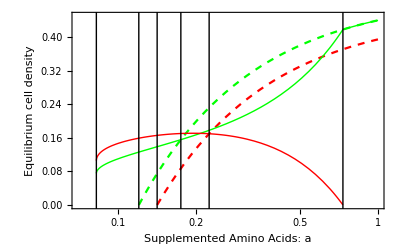

```mathematica
Xgra=LogLinearPlot[{fp3XNode,fp6XNode},{a,aMin,aMax},PlotStyle->{Directive[Green,Thick]},Frame->True,PlotRange->{0,0.7}];
Ygra=LogLinearPlot[{fp6YNode},{a,aMin,aMax},PlotStyle->{Directive[Red,Thick]},Frame->True,PlotRange->{0,0.45}];
eqvsaaGra=Show[Xmgra,Ymgra,Xgra,Ygra,Epilog-> thresh,FrameLabel->{"Supplemented Amino Acids: a","Equilibrium cell density"},PlotRange->{{Log[0.07],Log[1]},{0,0.45}}]
```

### Figure: Eigenvalues and eigenvector of fixed point

```mathematica
λ6a=1/2(tr6+√(tr6^2-4det6)); λ6b=1/2(tr6-√(tr6^2-4det6));
```

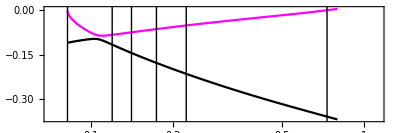

```mathematica
spvsaaGra=LogLinearPlot[{λ6a,λ6b},{a,.08,.8},Axes->True,Frame->True,Epilog->thresh,AxesOrigin->{0,0},PlotStyle->{Directive[Magenta],Directive[Black]},AspectRatio->1/3]
```

```mathematica
boxesAA={.085,.1066,.12,.3,.6};
```

```mathematica
figs=Line[{{Log[#],-.1},{Log[#],0}}]&/@boxesAA;
```

```mathematica
printBox[aa_]:=Module[{xRange=.4,yRange=.4},
fp6={X,Y}/.fp6val/.a->aa;
g6=Graphics[{PointSize[.04],Blue,Point[fp6]}];
J6at1=J6/.a->aa;
{{λeqa,λeqb},{veqa,veqb}}=J6at1//Eigensystem;
veqa2=veqa/(5 Norm[veqa]);veqb2=veqb/(5 Norm[veqb]);
veqaGra=Graphics[{Blue,Arrow[{fp6-veqa2/2,fp6+veqa2/2}]}];
veqbGra=Graphics[{Blue,Arrow[{fp6-veqb2/2,fp6+veqb2/2}]}];
Show[{g6,veqbGra},FrameLabel->{"X","Y"},PlotRange->{{0,xRange},{0,yRange}},Frame->True,AspectRatio->1]
]
```

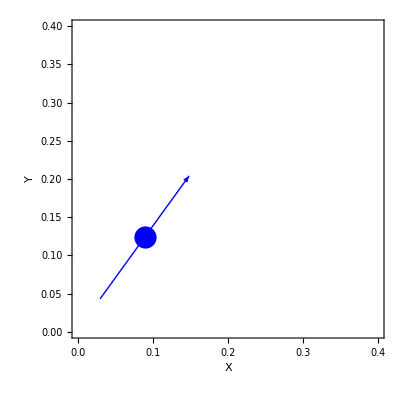
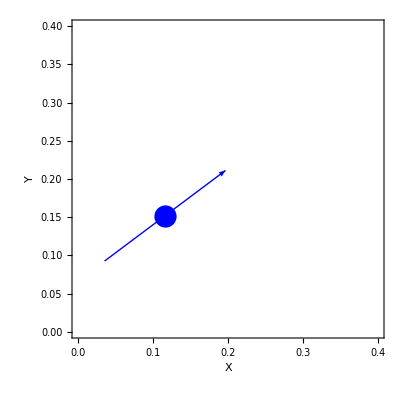
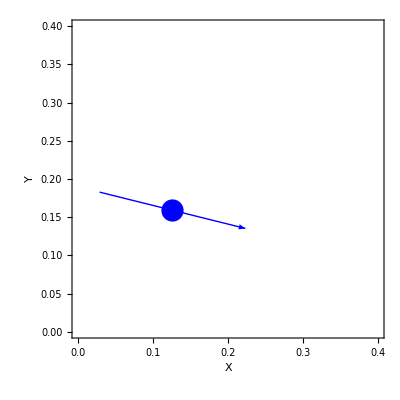
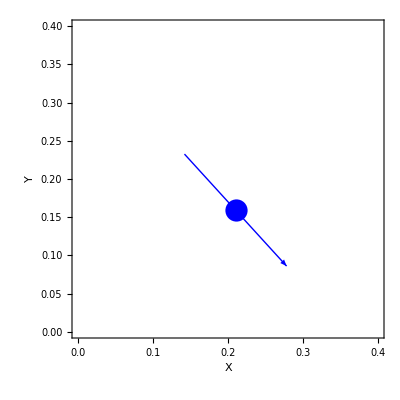
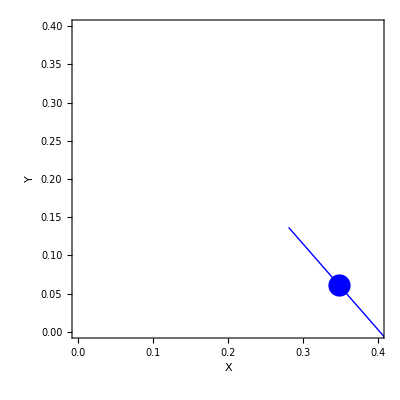

```mathematica
printBox/@boxesAA
```